2350508687/1048064

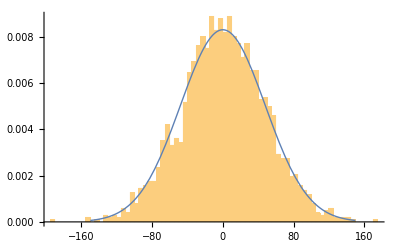

```mathematica
(*Approximating the probability distribution using the Central Limit Theorem with 'easy' sampling.*)

n=2^10;(*Degree of polynomial x^n+1*)
B=3;(*Bounding value of support*)

(*Applying the Central Limit Theorem to the n sums of the product coefficients.*)

numSums = 2^11;(*Number of trials to obtain the approximate distribution.*)
finalDistValues = Table[0,numSums];

For[m=1, m≤numSums, m++,
sum = 0;
For[l=1,l≤ n,l++,
e = 0;
s=0;
i=Table[Round[RandomVariate[UniformDistribution[{0,1}]]],2*B];(*Easy sampling.*)
j = Table[Round[RandomVariate[UniformDistribution[{0,1}]]],2*B];(*Easy sampling.*)
Do[e+=i[[k]]-i[[k+1]],{k,1,2*B-1,2}];
Do[s+=j[[k]]-j[[k+1]],{k,1,2*B-1,2}];
sum+=e*s;
];
finalDistValues[[m]]=sum;
]

(*Variance of final distribution.*)
Variance[finalDistValues]

(*Histogram of final distribution with approximating normal distribution N(0,48).*)
Show[Histogram[finalDistValues,50,"ProbabilityDensity"],Plot[PDF[NormalDistribution[0,48],x],{x,-150,150},PlotStyle->Thick]]
```